```mathematica
ClearAll["Global`*"]
```

The Jacobian at the internal steady state

[Note - I added a negative sign to recovery rates!!! Otherwise the rate is negative]

Plotting a distribution of Starvation rates vs. Hopf boundaries vs. TC boundaries as a function of increasing body mass and increasing parameter noise

Needs to be redone by calculating distance between Hopf curve and value vs. TC curve vs. value

```mathematica
TCMHfunc[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,ef_,γ_,ζ_,f0_,mm0_] :=(
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ];
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,σ];


growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;

TC = N[growth];
ValueSigma = N[starvation];
Hopf = N[HopfAnalytic/.{λ->growth,ρ->recovery,μ->mortality,m->maintenance,α->resourcegrowth}];
{TC,ValueSigma,Re[(σ/.Hopf)[[2]]]}
)
```

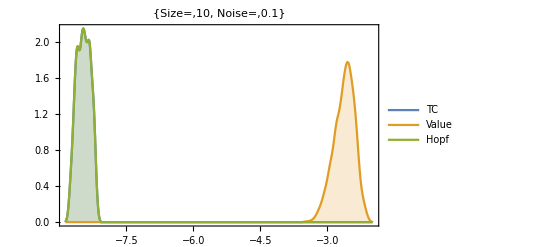
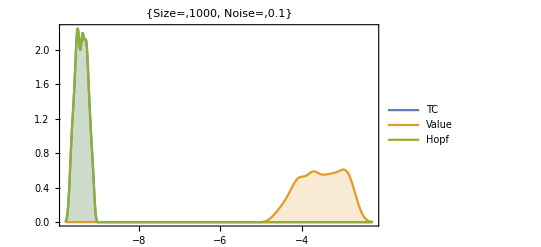
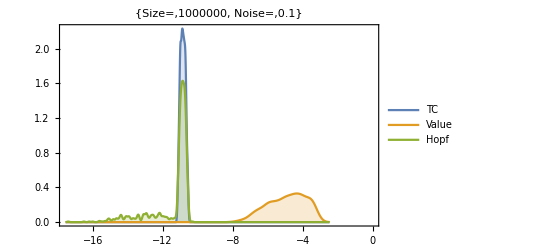
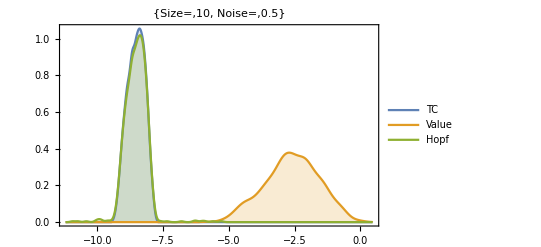
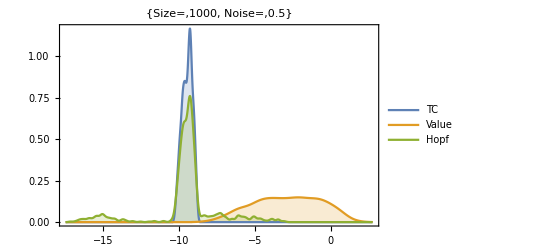
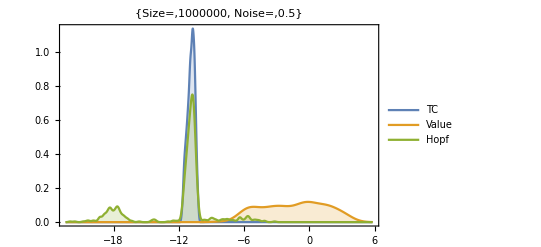

```mathematica
Table[
Table[
SigmaOutput=ParallelTable[
TCMHfunc[
(*ts*)1000,
(*M*)10^(y+RandomReal[{-0.5,0.5}]),
(*B0*)1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
(*Bm*)0.0245*(1+RandomReal[{-noise,noise}]),
(*Em*)21.39/2*1000(*J/gram*)*(1+RandomReal[{-noise,noise}]),
(*η*)3/4*(1+RandomReal[{-0,0}]),
(*η2*)-0.206*(1+RandomReal[{-0,0}]),
(*λ0*)3.3879*10^(-7)*(1+RandomReal[{-noise,noise}]),
(*ef*)0.01,
(*γ*)1.19*(1+RandomReal[{-noise,noise}]),
(*ζ*)1.01*(1+RandomReal[{-noise,noise}]),
(*f0*)0.0202*(1+RandomReal[{-noise,noise}]),
(*mm0*)0.324*(1+RandomReal[{-noise,noise}])
],{1000}];
SmoothHistogram[{Log[SigmaOutput[[All,1]]],Log[SigmaOutput[[All,2]]],Log[SigmaOutput[[All,3]]]},PlotLegends->{"TC","Value","Hopf"},Filling->Bottom,Frame->True,PlotLabel->{"Size=",10^y,"  Noise=",noise}],
{y,{1,3,6}}],{noise,{0.1,0.5}}]
```

Plotting vital rates as a function of Body Mass

```mathematica
Ratesfunc[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,ef_,γ_,ζ_,f0_,mm0_] :=(

growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
RatesByMass =
Table[
With[{noise=0.01},
R=Ratesfunc[
(*ts*)1000,
(*M*)Mass=10^(y+RandomReal[{-0.5,0.5}]),
(*B0*)1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
(*Bm*)0.0245*(1+RandomReal[{-noise,noise}]),
(*Em*)21.39/2*1000(*J/gram*)*(1+RandomReal[{-noise,noise}]),
(*η*)3/4*(1+RandomReal[{-noise,noise}]),
(*η2*)-0.206*(1+RandomReal[{-noise,noise}]),
(*λ0*)3.3879*10^(-7)*(1+RandomReal[{-noise,noise}]),
(*ef*)0.000001,
(*γ*)1.19*(1+RandomReal[{-noise,noise}]),
(*ζ*)1.01*(1+RandomReal[{-noise,noise}]),
(*f0*)0.0202*(1+RandomReal[{-noise,noise}]),
(*mm0*)0.324*(1+RandomReal[{-noise,noise}])
]];
{Mass,R},
{y,1,6,0.01}];
```

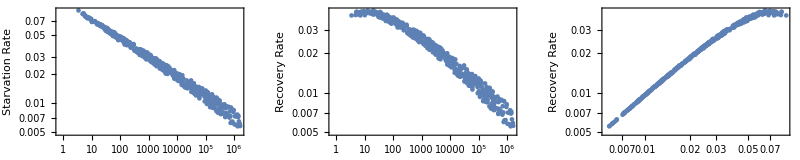

```mathematica
GraphicsGrid[{{
ListLogLogPlot[Transpose[{RatesByMass[[All,1]],RatesByMass[[All,2]][[All,2]]}],Frame->True,FrameLabel->{"Mass","Starvation Rate"}],
ListLogLogPlot[Transpose[{RatesByMass[[All,1]],RatesByMass[[All,2]][[All,4]]}],Frame->True,FrameLabel->{"Mass","Recovery Rate"}],
ListLogLogPlot[Transpose[{RatesByMass[[All,2]][[All,2]],RatesByMass[[All,2]][[All,4]]}],Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]
}},ImageSize->800]
```

Imaging the Hopf Bifurcation lines

```mathematica
HopfLinefunc[ts_,M_,B0_,Bm_,Em_,η_,η2_,λ0_,ef_,γ_,ζ_,f0_,mm0_] :=(
Jac = ({{ts*(λ-(1-R) σ), ts*R ρ, ts*H ρ+F σ}, {ts*(1-R) σ, ts*(-μ-R ρ), ts*(-H ρ-F σ)}, {ts*(-m R), ts*(-R ρ), ts*(-F m+(1-R) α-R α-H ρ)}});
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((m μ+λ ρ) (λ ρ+μ σ));

JacSpecSol = FullSimplify[Jac/.{R->Rstar, H->Hstar, F->Fstar}];
(*SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]*);
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
HopfAnalytic = Solve[Det[Sylv]==0,ρ];


growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;
(*Replace everything except rho and sigma to build the curve*)
(*HopfSol = HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth};*)
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,55}];
HopfSol = Table[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->growth,μ->mortality,m->maintenance,α->resourcegrowth,σ->sig})]]},{sig,sigvalues}];

out = {growth,HopfSol,starvation,recovery}
)
```

```mathematica
sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,55}]
```

{1.×10^-7,1.5×10^-7,2.25×10^-7,3.375×10^-7,5.0625×10^-7,7.59375×10^-7,1.13906×10^-6,1.70859×10^-6,2.56289×10^-6,3.84434×10^-6,5.7665×10^-6,8.64976×10^-6,0.0000129746,0.000019462,0.0000291929,0.0000437894,0.0000656841,0.0000985261,0.000147789,0.000221684,0.000332526,0.000498789,0.000748183,0.00112227,0.00168341,0.00252512,0.00378768,0.00568151,0.00852227,0.0127834,0.0191751,0.0287627,0.043144,0.064716,0.097074,0.145611,0.218416,0.327625,0.491437,0.737155,1.10573,1.6586,2.4879,3.73185,5.59777,8.39666,12.595,18.8925,28.3387,42.5081,63.7622,95.6432,143.465,215.197,322.796}

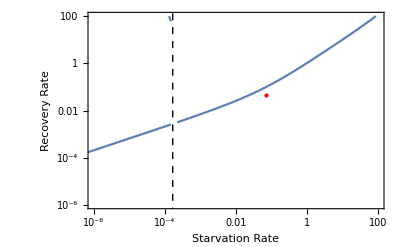

```mathematica
With[{noise=0.3,y=0.5},
Curve = HopfLinefunc[
(*ts*)1000,
(*M*)10^(y+RandomReal[{-0.5,0.5}]),
(*B0*)1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
(*Bm*)0.0245*(1+RandomReal[{-noise,noise}]),
(*Em*)21.39/2*1000(*J/gram*)*(1+RandomReal[{-noise,noise}]),
(*η*)3/4*(1+RandomReal[{0,0}]),
(*η2*)-0.206*(1+RandomReal[{0,0}]),
(*λ0*)3.3879*10^(-7)*(1+RandomReal[{-noise,noise}]),
(*ef*)0.000001,
(*γ*)1.19*(1+RandomReal[{-noise,noise}]),
(*ζ*)1.01*(1+RandomReal[{-noise,noise}]),
(*f0*)0.0202*(1+RandomReal[{-noise,noise}]),
(*mm0*)0.324*(1+RandomReal[{-noise,noise}])
];
Show[{
(*LogLogPlot[Curve[[2]],{σ,0.000001,100},PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"}]*)

ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,1]]}],PlotRange->{{0.000001,100},{0.000001,100}},Frame->True,FrameLabel->{"Starvation Rate","Recovery Rate"},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,2]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,3]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],
ListLogLogPlot[Transpose[{Curve[[2]][[All,1]],Curve[[2]][[All,2]][[All,4]]}],PlotRange->{{0.000001,100},{0.000001,100}},Joined->True],

Graphics[{Dashed,Line[{{Log@Curve[[1]],Log@0.0000001},{Log@Curve[[1]],1000}}]}],
Graphics[{Red,PointSize[Medium],Point[{Re[Log@Curve[[3]]],Re[Log@Curve[[4]]]}]}]
}]
]
```